## Theory Bandstructure

```mathematica
PM={IdentityMatrix[2],PauliMatrix[1],PauliMatrix[2],PauliMatrix[3]};
X[μ_]:=PM⟦μ+1⟧
X[μ_,ν_]:=KroneckerProduct[PM⟦μ+1⟧,PM⟦ν+1⟧]
X[μ_,ν_,ρ_]:=KroneckerProduct[PM⟦μ+1⟧,PM⟦ν+1⟧,PM⟦ρ+1⟧]
myConj[z_]:=z/.{Complex[a_,b_]->Complex[a,-b]}
zero2=ConstantArray[0,{2,2}];zero4=ConstantArray[0,{4,4}];
Hermitize[H_]:=(H+ConjugateTranspose[H])/2
```

```mathematica
SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[]
```

```mathematica
Hc[{kx_,ky_}]:=N[((-C11/2+CAz+α)*Cos[ky]-I*R*Cos[kx])*X[0]-(C1+Cy(2 Cos[ky-kx]) )X[1] - (C11/2+CAz - α) Cos[ky] X[3] /.{CAz->0.0150,α->-0.0150,C1->0.0150,C11->0.015,Cy->0.0075,R->0 }];
```

```mathematica
data = Table[SortBy[Eigenvalues[Hc[{kx,ky}]],Im],{kx,0,2π,2π/8},{ky,0,2π,2π/8}];
```

```mathematica
Transpose[data,{3,2,1}]//Dimensions
```

{2,9,9}

```mathematica
ListPlot3D[Transpose[data,{3,2,1}],AxesLabel->{"kx","ky","Energy"}]
```

-Graphics3D-

```mathematica
L=50;LBZ=50;
BZ=Table[i 2π/LBZ,{i,0,LBZ-1}];
```

```mathematica
Hhop1D[hop1_,k_]:=N[1/LBZ*Sum[Exp[-I k1 hop1](Hc[{k,k1}]),{k1,BZ}]];
PBC=False;
HOBC[k_]:=ArrayFlatten[ArrayFlatten[Table[Which[ix==jx ,Hhop1D[0,k],(jx==ix+1 )||(PBC&&jx==1&&ix==L),Hhop1D[1,k],(jx==ix-1 )||(PBC&&ix==1&&jx==L),Hhop1D[-1,k],True,0],{ix,L},{jx,L}]]];
```

```mathematica
obcdatacirc=ParallelTable[Eigenvalues[N[HOBC[k]]],{k,0,2π,2π/50}];
```

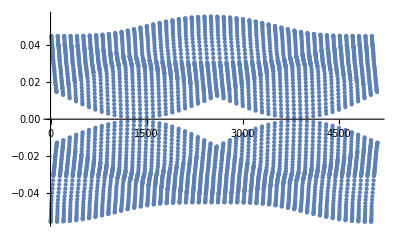

```mathematica
ListPlot[Transpose@Flatten@obcdatacirc, PlotStyle->PointSize[Medium]]
```

```mathematica
(* Following uses finite R *)
```

```mathematica
pbcdataAIIdag=Flatten@ParallelTable[Eigenvalues[N@Hc[{kx,ky}]],{kx,-π,π,π/100},{ky,-π,π,π/100}];
```

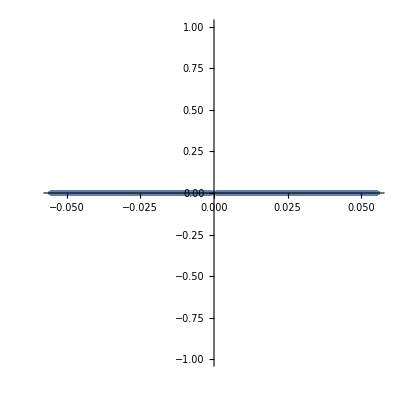

```mathematica
pbcplotAIIdag=ListPlot[Transpose[{Re@pbcdataAIIdag,Im@pbcdataAIIdag}],PlotStyle->{ColorData[97,"ColorList"][[1]],PointSize[Medium]}, AspectRatio->1, TicksStyle->Directive[FontOpacity->10,FontSize->0], PlotRange->Full]
```

```mathematica
CheckSymmetriesdim2[Hc]
```

CheckSymmetriesdim2[Hc]

```mathematica
L=16;LBZ=16;
BZ=Table[i 2π/LBZ,{i,0,LBZ-1}];
```

```mathematica
Hhop1D[hop1_,k_]:=N[1/LBZ*Sum[Exp[-I k1 hop1](Hc[{k,k1}]),{k1,BZ}]];
PBC=False;
HOBCDIII[k_]:=ArrayFlatten[ArrayFlatten[Table[Which[ix==jx ,Hhop1D[0,k],(jx==ix+1 )||(PBC&&jx==1&&ix==L),Hhop1D[1,k],(jx==ix-1 )||(PBC&&ix==1&&jx==L),Hhop1D[-1,k],True,0],{ix,L},{jx,L}]]];
```

```mathematica
obcdataAIIdag=ParallelTable[Eigenvalues[N[HOBCDIII[k]]],{k,0,2π,2π/50}];
```

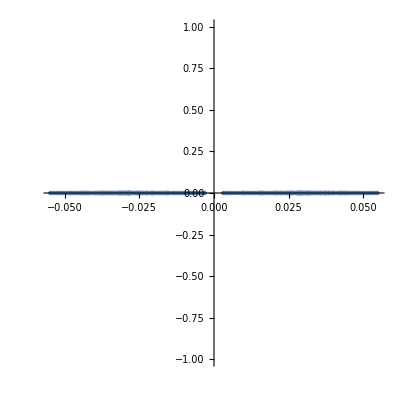

```mathematica
obcplotAIIdag=ListPlot[Transpose[{Re@Flatten@obcdataAIIdag,Im@Flatten@obcdataAIIdag}],PlotStyle->{ColorData[97,"ColorList"][[1]],PointSize[Medium]}, AspectRatio->1, TicksStyle->Directive[FontOpacity->10,FontSize->0], PlotRange->Full]
```

## Measurement Bandstructure

```mathematica
(*importedVoltagesPath = "C:\\Users\\Nelson's Laptop\\OneDrive - Universität Zürich UZH\\University\\Master\\MLA Data\\Board_2_Repaired_Complete_Measurement_Inputs_(4,4,2)_230111\\";*)
importedVoltagesPath = "C:\\Users\\Nelson's Laptop\\OneDrive - Universität Zürich UZH\\University\\Master\\MLA Data\\Board_2_Complete_Measurement_Inputs_(4,4,2)_221107\\";
importedVoltages = Import[#,"Table"]&/@(FileNames[importedVoltagesPath<>"\\Voltages_*.txt"]);
```

```mathematica
p1=Flatten[Table[{{5-p,5-q,1,2},{5-p,5-q,1,1}},{p,1,4},{q,1,4}],2];
p2=Flatten[Table[{{9-p,5-q,1,2},{9-p,5-q,1,1}},{p,1,4},{q,1,4}],2];
p3=Flatten[Table[{{4+p,4+q,1,1},{4+p,4+q,1,2}},{p,1,4},{q,1,4}],2];
p4=Flatten[Table[{{p,4+q,1,1},{p,4+q,1,2}},{p,1,4},{q,1,4}],2];
correspondingNodeCoords=Join[p1,p2,p3,p4];

reorderingPos = {Flatten[Table[Position[correspondingNodeCoords,{x,y,1,1}][[1,1]],{x,1,8},{y,1,8}],1],Flatten[Table[Position[correspondingNodeCoords,{x,y,1,2}][[1,1]],{x,1,8},{y,1,8}],1]};

NUnit=8;

shuntR = 10.853;

input ={4,4};

inputValues = {0.0026585388963521655+0.0002615716921686406 ⅈ,0.0024380098788940392+0.0007765094180627827 ⅈ};

inputPos ={Position[correspondingNodeCoords,{input[[1]],input[[2]],1,1}][[1,1]],Position[correspondingNodeCoords,{input[[1]],input[[2]],1,2}][[1,1]]};
```

```mathematica
voltagesV1=Table[(importedVoltages[[1,reorderingPos[[sub,node]]+2+(2-subInput)*130,2]])*Exp[I*importedVoltages[[1,reorderingPos[[sub,node]]+2+(2-subInput)*130,3]]],{subInput,1,2},{sub,1,2},{node,1,64}];

voltagesV2=Table[(importedVoltages[[1,reorderingPos[[sub,node]]+2+(2-subInput)*130,4]])*Exp[I*importedVoltages[[1,reorderingPos[[sub,node]]+2+(2-subInput)*130,5]]],{subInput,1,2},{sub,1,2},{node,1,64}];

currentVector =Table[If[reorderingPos[[sub,node]]==inputPos[[sub]],inputValues[[sub]],0],{sub,1,2},{node,1,64}];
```

```mathematica
fourierVoltagesV1 = Table[∑_(l=1)^NUnit ( ∑_(j=1)^NUnit voltagesV1[[subInput,sub,((j-1)*NUnit)+l]]*Exp[-ⅈ*2*π*kx*j/NUnit])*Exp[-ⅈ*2*π*ky*l/NUnit],{subInput,1,2},{sub,1,2},{kx,1,8},{ky,1,8}];

fourierVoltagesV2 = Table[∑_(l=1)^NUnit ( ∑_(j=1)^NUnit voltagesV2[[subInput,sub,((j-1)*NUnit)+l]]*Exp[-ⅈ*2*π*kx*j/NUnit])*Exp[-ⅈ*2*π*ky*l/NUnit],{subInput,1,2},{sub,1,2},{kx,1,8},{ky,1,8}];

fourierCurrentVector = Table[∑_(l=1)^NUnit ( ∑_(j=1)^NUnit currentVector[[sub,((j-1)*NUnit)+l]]*Exp[-ⅈ*2*π*kx*j/NUnit])*Exp[-ⅈ*2*π*ky*l/NUnit],{sub,1,2},{kx,1,8},{ky,1,8}];
```

```mathematica
Detk=Table[ (fourierVoltagesV2[[1,1,kx,ky]]*fourierVoltagesV2[[2,2,kx,ky]])/(fourierCurrentVector[[1,kx,ky]]*fourierCurrentVector[[2,kx,ky]])-(fourierVoltagesV2[[1,2,kx,ky]]*fourierVoltagesV2[[2,1,kx,ky]])/(fourierCurrentVector[[1,kx,ky]]*fourierCurrentVector[[2,kx,ky]]),{kx,1,8},{ky,1,8}];

Lap = Table[1/Detk[[kx,ky]]*{{fourierVoltagesV2[[2,2,kx,ky]]/fourierCurrentVector[[2,kx,ky]],-fourierVoltagesV2[[2,1,kx,ky]]/fourierCurrentVector[[2,kx,ky]]},{-fourierVoltagesV2[[1,2,kx,ky]]/fourierCurrentVector[[1,kx,ky]],fourierVoltagesV2[[1,1,kx,ky]]/fourierCurrentVector[[1,kx,ky]]}},{kx,1,8},{ky,1,8}];
```

```mathematica
Detk2=Table[ (fourierVoltagesV1[[1,1,kx,ky]]*fourierVoltagesV1[[2,2,kx,ky]])/(fourierCurrentVector[[1,kx,ky]]*fourierCurrentVector[[2,kx,ky]])-(fourierVoltagesV1[[1,2,kx,ky]]*fourierVoltagesV1[[2,1,kx,ky]])/(fourierCurrentVector[[1,kx,ky]]*fourierCurrentVector[[2,kx,ky]]),{kx,1,8},{ky,1,8}];

Lap2 = Table[1/Detk2[[kx,ky]]*{{fourierVoltagesV1[[2,2,kx,ky]]/fourierCurrentVector[[2,kx,ky]],-fourierVoltagesV1[[2,1,kx,ky]]/fourierCurrentVector[[2,kx,ky]]},{-fourierVoltagesV1[[1,2,kx,ky]]/fourierCurrentVector[[1,kx,ky]],fourierVoltagesV1[[1,1,kx,ky]]/fourierCurrentVector[[1,kx,ky]]}},{kx,1,8},{ky,1,8}];
```

```mathematica
LapEigenvalues = Im[Table[SortBy[Eigenvalues[Lap[[kx,ky]]],Im],{kx,1,8},{ky,1,8}]];

LapEigenvalues2 = Im[Table[SortBy[Eigenvalues[Lap2[[kx,ky]]],Im],{kx,1,8},{ky,1,8}]];
```

```mathematica
kTicks = Table[{k,(k-1)(2π)/NUnit},{k,1,8,2}];

ListPlot3D[Transpose[LapEigenvalues,{3,2,1}],AxesLabel->{"ky","kx",Rotate["Laplacian Eigenvalues",90 Degree]},Ticks->{kTicks,kTicks,Automatic},PlotRange->All,ImageSize->Large,PlotLabel->Style["Experimental Coil Replaced Single Layer Bandstructure",Bold,15],ViewPoint->{0,1,0}]

ListPlot3D[Transpose[LapEigenvalues2,{3,2,1}],AxesLabel->{"ky","kx","Laplacian Eigenvalues"},Ticks->{kTicks,kTicks,Automatic},PlotRange->All,ImageSize->Large];
```

-Graphics3D-

```mathematica
L1Value = 27*10^-6;
L2Value = 5.6*10^-6;
L3Value = 27*10^-6;

C1Value = 150*10^-12;
C2Value = 75*10^-12;
C3Value = 150*10^-12;

Ry = 15.92;


ltSpiceFreq = -51;

frequency = 2.38*10^6;

Acap =True;
Bcap = True;
Sandwich = True;

systemLengthX = NUnit;
systemLengthY = NUnit;
systemLengthZ = 1;

jMatrix[kx_,ky_]:= {{C1Value+2C2Value+2C3Value,0},{0,C1Value+2C2Value-2/((2π*frequency)^2 L1Value)}}-{{2*C3Value*Cos[ky],C1Value+2C2Value*Cos[ky-kx]},{C1Value+2C2Value*Cos[ky-kx],-2/((2π*frequency)^2*L1Value)Cos[ky]}}+{{If[Sandwich==True && Acap==True,C1Value,0]-1/((2π*frequency)^2 L2Value),0},{0,If[Sandwich==True && Bcap==True,C1Value,0]-1/((2π*frequency)^2 L3Value)}};
```

```mathematica
kTicksTheo = Table[{2k,2(k-1)(2π)/NUnit},{k,1,4}];

data = Table[SortBy[Eigenvalues[jMatrix[kx,ky]],Im],{kx,0,2π,2π/NUnit},{ky,0,2π,2π/NUnit}];

ListPlot3D[Transpose[data,{3,2,1}],AxesLabel->{"ky","kx",Rotate["Energy Eigenvalues",90 Degree]},Ticks->{kTicksTheo,kTicksTheo,Automatic},PlotRange->All,ImageSize->Large,PlotLabel->Style["Theoretical Single Layer Bandstructure",Bold,15],ViewPoint->{0, 1, 0}]
```

-Graphics3D-

```mathematica
xcords=Join[Subdivide[0,Pi,4],Subdivide[Pi,Pi,4-1],Subdivide[3 Pi/4,0,4-1],Subdivide[0,0,4-1]];

ycords=Join[Subdivide[0,0,4],Subdivide[Pi/4,Pi,4-1],Subdivide[Pi,Pi,4-1],Subdivide[3 Pi/4,0,4-1]];

pathTheoretical=Table[{xcords[[i]],ycords[[i]]},{i,1,Length[xcords]}];
```

```mathematica
LapBandPathValsTheory=Im[Table[SortBy[Eigenvalues[Lap[[4/π *pathTheoretical[[i,1]]+1,1+4/π *pathTheoretical[[i,2]]]]],Im],{i,1,Length[pathTheoretical]}]];

BandPathValsTheory=15000*Table[SortBy[Eigenvalues[jMatrix[pathTheoretical[[i,1]],pathTheoretical[[i,2]]]],Re],{i,1,Length[pathTheoretical]}];
```

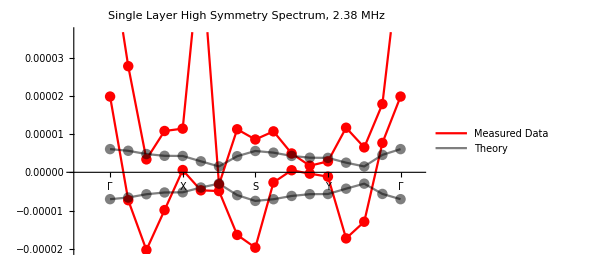
-Graphics-Hamiltonian Eigenvalues E_n

```mathematica
Frequency = frequency;

Labeled[ListLinePlot[{LapBandPathValsTheory[[;;,1]],LapBandPathValsTheory[[;;,2]],BandPathValsTheory[[;;,1]],BandPathValsTheory[[;;,2]]},Mesh->All,PlotRange->{{-1,18},Automatic},PlotLegends->{"Measured Data",None,"Theory",None},PlotStyle->{Red,Red,{Black,Opacity[0.5]},{Black,Opacity[0.5]}},PlotLabel->"Single Layer High Symmetry Spectrum, "<>ToString[Frequency/(10^6)]<>" MHz",PlotStyle->{Black,Black},AxesOrigin->{-1,0},Ticks->{{{1,"Γ"},{5,"X"},{9,"S"},{13,"Y"},{17,"Γ"}},Automatic},ImageSize->450],{"","Hamiltonian Eigenvalues E_n"},{Bottom,Left},RotateLabel->True]
```

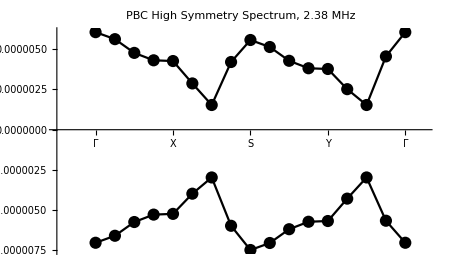
-Graphics-Hamiltonian Eigenvalues E_n

```mathematica
Labeled[ListLinePlot[{BandPathValsTheory[[;;,1]],BandPathValsTheory[[;;,2]]},Mesh->All,PlotRange->{{-1,18},Automatic},PlotLabel->"PBC High Symmetry Spectrum, "<>ToString[Frequency/(10^6)]<>" MHz",PlotStyle->{Black,Black},AxesOrigin->{-1,0},Ticks->{{{1,"Γ"},{5,"X"},{9,"S"},{13,"Y"},{17,"Γ"}},Automatic},ImageSize->450],{"","Hamiltonian Eigenvalues E_n"},{Bottom,Left},RotateLabel->True]
```